## PLLs

```mathematica
(* -Graphics-;
-Graphics-; -Graphics- & -Graphics-*)
Clear[ξ,rt,s,a0,sign,en,ζ,B,vx,vy];
rt[ξ_,kx_]=a0(3/2+(ξ kx a0)/4);s[ξ_,kx_]=1+(ξ kx a0)/2;ζ= (*e *) B vx/vy;
ass=Assumptions->{ξ,a0,sign,B,vx,vy,a0,rat}∈Reals &&  a0>0 && vx>0 && vy>0 && a0>0 && rat>0;
repl={vx->Subscript[v, x],vy->Subscript[v, y],kx->Subscript[k, x],ky->Subscript[k, y],σx->Subscript[σ, x],σy->Subscript[σ, y],ηx->Subscript[η, x],a0->Subscript[a, 0]};
```

```mathematica
(*-Graphics-*)
Clear[kx,ham,jx, jxsc];
sx=PauliMatrix[1];sy=PauliMatrix[2];
ham[ξ_]=vx ηx kx IdentityMatrix[2](**)+vx (ξ kx+s[-ξ,kx]e B y) (**)sx+vy ky (s[ξ,kx]-e B y rt[ξ,kx])(**)sy;

jx[ξ_]=D[ham[ξ],kx]//FullSimplify;
jxsc[ξ_]=jx[ξ]/vx/.{kx->kxsc/a0,ky->-ⅈ Dysc/a0,B->Bsc/(a0 a0), y->ysc a0, vy->rat vx}//FullSimplify;

MatrixForm[jxsc[ξ]]
Print["ham"];
Series[vx ηx kx id(**)+vx (ξ kx+s[-ξ,kx]e B y) (**)σx+vy ky (s[ξ,kx]-e B y rt[ξ,kx])(**)σy//FullSimplify,{σx,0,1},{σy,0,1}]//FullSimplify//Normal
Print["jx"];
Series[D[vx ηx kx id(**)+vx (ξ kx+s[-ξ,kx]e B y) (**)σx+vy ky (s[ξ,kx]-e B y rt[ξ,kx])(**)σy,kx]//FullSimplify,{σx,0,1},{σy,0,1}]//FullSimplify//Normal
```

(ηx | 1/4 (-2+Dysc rat) (-2+Bsc e ysc) ξ
-1/4 (2+Dysc rat) (-2+Bsc e ysc) ξ | ηx)

ham

id kx vx ηx+vx (kx ξ+B e y (1-(a0 kx ξ)/2)) σx+1/4 ky vy (4+2 a0 kx ξ-a0 B e y (6+a0 kx ξ)) σy

jx

id vx ηx-1/2 vx (-2+a0 B e y) ξ σx-1/4 a0 ky vy (-2+a0 B e y) ξ σy

```mathematica
exp=vx ηx-1/2 vx (-2+a0 B e y) ξ σx-1/4 a0 ky vy (-2+a0 B e y) ξ σy/.repl;
TeXForm[exp]
```

```mathematica
enex=Simplify[Simplify[vx/1(ηx kx + sign √(rt[ξ,kx]^2(Abs[ζ]n+((*e*)B+Abs[ζ])/2)^2+(kx rt[ξ,kx]+s[-ξ,kx]s[ξ,kx])(2Abs[ζ]n+(*e*)B+Abs[ζ])))]/.{kx->kxsc/a0,B->Bsc/(a0 a0),vy->rat vx},ass]

en[ξ_,ηx_,kxsc_,n_,sign_,{vx_,vy_},Bsc_]= a0  enex/vx
(* Plotting 8 a0  energy/vx versus a0 Kx, expressing with the help of Bsc = B a0^2*)
```

(vx (8 kxsc ηx+sign √(((Bsc rat+Abs[Bsc]+2 n Abs[Bsc]) (64+96 kxsc-16 kxsc^2 (-1+ξ) ξ+(6+kxsc ξ)^2 (Bsc+((1+2 n) Abs[Bsc])/rat)))/rat)))/(8 a0)

1/8 (8 kxsc ηx+sign √(((Bsc rat+Abs[Bsc]+2 n Abs[Bsc]) (64+96 kxsc-16 kxsc^2 (-1+ξ) ξ+(6+kxsc ξ)^2 (Bsc+((1+2 n) Abs[Bsc])/rat)))/rat))

```mathematica
Clear[en];en[ξ_,ηx_,kxsc_,n_,sign_,rat_,Bsc_]=kxsc ηx+sign/8 √(((Bsc rat+Abs[Bsc]+2 n Abs[Bsc]) (64+96 kxsc-16 kxsc^2 (-1+ξ) ξ+(6+kxsc ξ)^2 (Bsc+((1+2 n) Abs[Bsc])/rat)))/rat);
(* Plotting 8 a0  energy/vx versus a0 Kx, expressing with the help of Bsc = B a0^2*)
```

0.

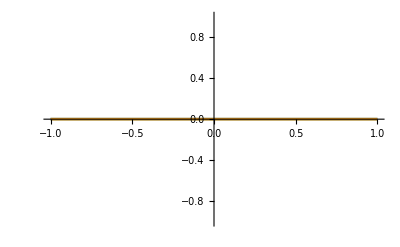

```mathematica
Bval=-1*10^(-2); lim=20;etaval=0.5 0;
ratval= 1;
en[1,etaval,kx,0,1,ratval,Bval]
Plot[{en[1,etaval,kx,0,1,ratval,Bval],en[1,etaval,kx,0,-1,ratval,Bval]},{kx,-1,1}]
```

## Plots: LLs

```mathematica
Bval=1*10^(-2); lim=20;
 rati=1/9;
styles={Directive[Orange,Thickness[0.004]],Directive[Blue,Thickness[0.004]]};
(**************)
 etaval =  0.9;
(************)
Clear[Energy,p1,p2];
Energy[kx_,n_,sign_]=en[1,etaval,kx,n,sign,rati,Bval];
Energy[1,1,1]

(* valley D*)
p1[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,20}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {+, 0.9, 1/9, 10^-2} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}](* {{left,right},{bottom,top}}*)

Clear[Energy];
Energy[kx_,n_,sign_]=en[-1,etaval,kx,n,sign,rati,Bval];
Energy[1,1,1]

(* valley D'*)
p2[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,35}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {-, 0.9, 1/9, 10^-2}",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}]


uplim=4;
s1=Show[{p1[1,{2,uplim}],p1[-1,{2,uplim}]}];
s2=Show[{p2[1,{3.5,uplim}],p2[-1,{3.5,uplim}]}];
(* for negative ηx *)
(**************)
 etaval = -etaval;
(************)
Clear[Energy,p1,p2];
Energy[kx_,n_,sign_]=en[1,etaval,kx,n,sign,rati,Bval];
Energy[1,1,1]

p1[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,ni,sign],{ni,0,20}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {+, -0.9, 1/9, 10^-2} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}];

Clear[Energy];
Energy[kx_,n_,sign_]=en[-1,etaval,kx,n,sign,rati,Bval];
Energy[1,1,1]


p2[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,35}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {-, -0.9, 1/9, 10^-2} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}];


uplim=4;
s11=Show[{p1[1,{2,uplim}],p1[-1,{2,uplim}]}];
s12=Show[{p2[1,{3.5,uplim}],p2[-1,{3.5,uplim}]}];
allpl=GraphicsGrid[{{s1,s2},{s11,s12}},Spacings->{20,20},ImageSize->1000]
```

1.77179

1.66852

-0.0282059

-0.131479

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figPLL.pdf",Rasterize[allpl, Background->None],ImageResolution->500,ImageSize->500];
```

### negative B, equal vel

```mathematica
Bval=-1*10^(-2); lim=20;
 rati=1;
styles={Directive[Orange,Thickness[0.004]],Directive[Blue,Thickness[0.004]]};
(**************)
 etaval =  0.9;
(************)
Clear[Energy,p1,p2];
Energy[kx_,n_,sign_]=en[1,etaval,kx,n,sign,rati,Bval];
Energy[1,1,1]

(* valley D*)
p1[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,1,20}]]},{k,-lim1,lim2},PlotStyle->{styles[[sign/2+3/2]]},PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {+, 0.9, 1, -10^-2} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}},ImagePadding->{{80,Automatic}, {Automatic, 10}}](* {{left,right},{bottom,top}}*)

Clear[Energy];
Energy[kx_,n_,sign_]=en[-1,etaval,kx,n,sign,rati,Bval];
Energy[1,1,1]

(* valley D'*)
p2[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,35}]]},{k,-lim1,lim2},PlotStyle->{styles[[sign/2+3/2]]},PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {-, 0.9, 1, -10^-2}",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}},ImagePadding->{{80,Automatic}, {Automatic, 10}}];

uplim=3.65;
s1=Show[p1[1,{2,uplim}],p1[-1,{2,uplim}],(**)Plot[Energy[k,0,1],{k,-2,uplim},PlotStyle->Red,PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {+, 0.9, 1, -10^-2} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 40}}](**)];

s2=Show[p2[1,{2,uplim}],p2[-1,{2,uplim}],(**)Plot[Energy[k,0,1],{k,-2,uplim},PlotStyle->Red,PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {-, 0.9, 1, -10^-2} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 40}}](**)]
(* for negative ηx *)
(**************)
 etaval = -etaval;
(************)
Clear[Energy,p1,p2];
Energy[kx_,n_,sign_]=en[1,etaval,kx,n,sign,rati,Bval];
Energy[1,1,1]

p1[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,ni,sign],{ni,1,20}]]},{k,-lim1,lim2},PlotStyle->{styles[[sign/2+3/2]]},PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {+, -0.9, 1, -10^-2} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}];

Clear[Energy];
Energy[kx_,n_,sign_]=en[-1,etaval,kx,n,sign,rati,Bval];
Energy[1,1,1]


p2[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,1,35}]]},{k,-lim1,lim2},PlotStyle->{styles[[sign/2+3/2]]},PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {-, -0.9, 1, -10^-2} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 10}}];

s11=Show[p1[1,{2,uplim}],p1[-1,{2,uplim}],(**)Plot[Energy[k,0,1],{k,-2,uplim},PlotStyle->Red,PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {-, -0.9, 1, -10^-2} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 40}}](**)];


(*****************)
s12=Show[p2[1,{2,uplim}],p2[-1,{2,uplim}],(**)Plot[Energy[k,0,1],{k,-2,uplim},PlotStyle->Red,PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × a_0/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x, v_y/v_x, a_0^2 ℬ} = {-, -0.9, 1, -10^-2} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic,ImagePadding->{{80,Automatic}, {Automatic, 40}}](**)];
allpl=GraphicsGrid[{{s1,s2},{s11,s12}},Spacings->{20,20},ImageSize->1000]
```

1.12429

1.10039

-0.675709

-0.69961

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figPLL2.pdf",Rasterize[allpl, Background->None],ImageResolution->500,ImageSize->500];
```

## untilted

6.97435

6.14817

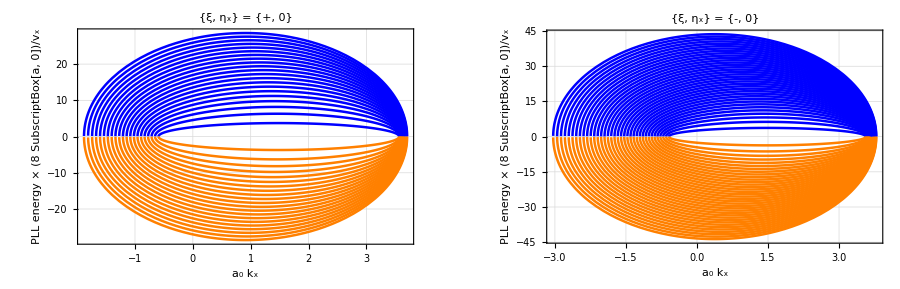

```mathematica
Bval=1*10^(-2); lim=20;
vxval=0.001; vyval= vxval/9;
styles={Directive[Orange,Thickness[0.004]],Directive[Blue,Thickness[0.004]]};
(**************)
 etaval =  0;
(************)
Clear[Energy,p1,p2];
Energy[kx_,n_,sign_]=en[1,etaval,kx,n,sign,{vxval,vyval},Bval];
Energy[1,1,1]

(* valley D*)
p1[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,20}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × (8 SubscriptBox[a, 0])/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x} = {+, 0} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic];
Clear[Energy];
Energy[kx_,n_,sign_]=en[-1,etaval,kx,n,sign,{vxval,vyval},Bval];
Energy[1,1,1]

(* valley D'*)
p2[sign_,{lim1_,lim2_}]:=Plot[{Evaluate[Table[Energy[k,i,sign],{i,0,35}]]},{k,-lim1,lim2},PlotStyle->styles[[sign/2+3/2]],PlotRange->All,Axes->None,BaseStyle->{Bold,22,FontFamily->"Times"},Frame-> True,LabelStyle->Directive[Black],FrameLabel-> {Style["a_0 k_x",22,Bold,FontFamily->"Times"],Style["PLL energy × (8 SubscriptBox[a, 0])/v_x",19,FontFamily->"Times"]},FrameTicksStyle->Directive[Darker[Gray],16],ImageSize->450,PlotLabel->Style["{ξ, η_x} = {-, 0} ",FontFamily->"Times",Bold,Darker[Brown],18],GridLines->Automatic];

uplim=4;
s1=Show[{p1[1,{2,uplim}],p1[-1,{2,uplim}]}];
s2=Show[{p2[1,{3.5,uplim}],p2[-1,{3.5,uplim}]}];
allpl=GraphicsGrid[{{s1,s2}},Spacings->{40,40},ImageSize->900]
SetDirectory[NotebookDirectory[]];
Export["figPLL-notilt.pdf",Rasterize[allpl, Background->None],ImageResolution->250,ImageSize->250];
```

## wvfns

### smooth approx. of Heaviside Θ

```mathematica
(*-Graphics-; -Graphics-*)
```

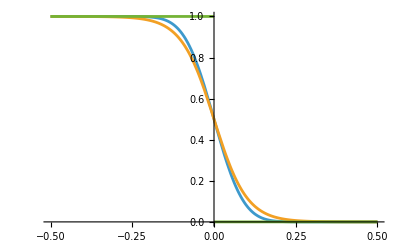

```mathematica
par=10;Plot[{(1+Erf[par(-y)])/2,1/(1+ⅇ^(-2par(-y))),HeavisideTheta[-y]},{y,-0.5,0.5}]
```

### gen Laguerre poly

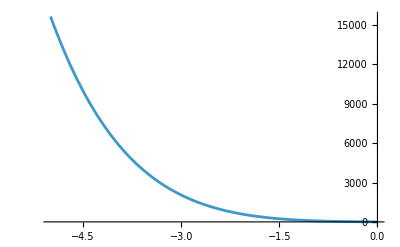

```mathematica
(* -Graphics- *)
Plot[LaguerreL[9,0.5,yt],{yt,-5,0}]
```

```mathematica
(* -Graphics- *)
(* -Graphics-;
-Graphics-; -Graphics- & -Graphics-*)
Clear[ξ,a0,sign,B,vx,vy,fn,ϕB,ϕA,ysg];

ass=Assumptions->{ξ,a0,sign,B,vx,vy,a0,rat}∈Reals &&  a0>0 && vx>0 && vy>0 && a0>0 && rat>0;
rt[ξ_,kx_]=a0(3/2+(ξ kx a0)/4);s[ξ_,kx_]=1+(ξ kx a0)/2;ζ= (*e *) B vx/vy;
ysg[ξ_,kxsc_,Bsc_]=FullSimplify[s[ξ,kx]/(rt[ξ,kx]a0(*e*)B)/.{kx->kxsc/a0,B->Bsc/(a0 a0), y->ysc a0, vy->rat vx}];
sqrtD[ξ_,kx_, n_]=-rt[ξ,kx]^2 (*e*)(vy Abs[B])/vx n+kx rt[ξ,kx]-rt[ξ,kx]^2/2((*e*)B +(vy Abs[B])/vx )+s[ξ,kx]s[-ξ,kx];
α[ξ_,kxsc_,Bsc_,y_]:=(4 vx y (-2+a0 kxsc ξ) Sign[Bsc])/(a0 vy (6+a0 kxsc ξ));
(***************************)

ϕB[a0_,ysc_,ξ_,kxsc_,Bsc_, n_,rat_]=Simplify[(**)Exp[(2 vx Sign[B]s[-ξ,kx]y)/(vy rt[ξ,kx])] y^(-1/2+(vx sqrtD[ξ,kx, n])/(rt[ξ,kx]^2(*e*) vy Abs[B]))*LaguerreL[n,(2vx sqrtD[ξ,kx, n])/(-rt[ξ,kx]^2(*e*)vy Abs[B]),(-2vx Sign[B]s[-ξ,kx] y)/(rt[ξ,kx](*e*)vy)]/.{kx->kxsc/a0,B->Bsc/(a0 a0), y->ysc a0, vy->rat vx},ass(**)]
(***********************************************************************)

ϕA[a0_,vx_,ysc_,ξ_,kxsc_,Bsc_,n_,rat_]=Simplify[(**)(ⅇ^(-(2 vx y (-2+s[ξ,kx]) Sign[B])/(vy rt[ξ,kx])) y^(-2-n-(vx (B+(-4+a0 kx (-6+a0 kx (-1+ξ) ξ))/(2 rt[ξ,kx]^2)))/(2 vy Abs[B])) (-LaguerreL[n,1+2 n+(vx (-32-48 a0 kx+12 a0^3 B kx ξ+a0^4 B kx^2 ξ^2+4 a0^2 (9 B+2 kx^2 (-1+ξ) ξ)))/(16 vy Abs[B] rt[ξ,kx]^2),α[ξ,kx,B,y]] (8 vx (-4-6 a0 kx+a0^2 kx^2 (-1+ξ) ξ+2 B rt[ξ,kx]^2) (4 a0 B y rt[ξ,kx]+4 vy (-2+s[ξ,kx]))+8 rt[ξ,kx] (4 vy Abs[B] rt[ξ,kx] (6 a0^2 B (1+n) y+kx (a0^3 B (1+n)-4 vx) y ξ+4 (1+n) vy (-2+s[ξ,kx]))+8 B vx y (y rt[ξ,kx] (-8 a0 B-2 vy+a0 vy ξ+4 a0 B s[ξ,kx])+4 vy (-1+s[-ξ,kx] s[ξ,kx]))))-256 vx y Abs[B] LaguerreL[-1+n,2 (1+n)+(vx (-32-48 a0 kx+12 a0^3 B kx ξ+a0^4 B kx^2 ξ^2+4 a0^2 (9 B+2 kx^2 (-1+ξ) ξ)))/(16 vy Abs[B] rt[ξ,kx]^2),α[ξ,kx,B,y]] rt[ξ,kx] (a0 B y rt[ξ,kx]+vy (-2+s[ξ,kx])) (-2+s[ξ,kx]) Sign[B]))/(64 vx vy Abs[B] rt[ξ,kx]^2 √((B+Abs[ζ]+2 n Abs[ζ]) (4+6 a0 kx-a0^2 kx^2 (-1+ξ) ξ+(B+Abs[ζ]+2 n Abs[ζ]) rt[ξ,kx]^2)) Sign[B])/.{kx->kxsc/a0,B->Bsc/(a0 a0), y->ysc a0, vy->rat vx},ass(**)]
```

ⅇ^(-(4 ysc (-2+kxsc ξ) Sign[Bsc])/(rat (6+kxsc ξ))) (a0 ysc)^(-1-n+(32+48 kxsc-8 kxsc^2 (-1+ξ) ξ-Bsc (6+kxsc ξ)^2)/(2 rat (6+kxsc ξ)^2 Abs[Bsc])) LaguerreL[n,1+2 n+Bsc/(rat Abs[Bsc])+(8 (-4-6 kxsc+kxsc^2 (-1+ξ) ξ))/(rat (6+kxsc ξ)^2 Abs[Bsc]),(4 ysc (-2+kxsc ξ) Sign[Bsc])/(rat (6+kxsc ξ))]

(a0 ⅇ^(-(4 ysc (-2+kxsc ξ) Sign[Bsc])/(rat (6+kxsc ξ))) (a0 ysc)^(-2-n+(32+48 kxsc-8 kxsc^2 (-1+ξ) ξ-Bsc (6+kxsc ξ)^2)/(2 rat (6+kxsc ξ)^2 Abs[Bsc])) (-((8 vx (2 rat vx (-2+kxsc ξ)+a0 Bsc ysc (6+kxsc ξ)) (-4-6 kxsc+kxsc^2 (-1+ξ) ξ+1/8 Bsc (6+kxsc ξ)^2)+2 vx (6+kxsc ξ) (2 Bsc ysc (-4 kxsc^2 rat vx ξ^2-2 a0^2 rat vx ysc (6+kxsc ξ)+a0^3 rat vx ysc ξ (6+kxsc ξ)+2 a0 Bsc ysc (-12+4 kxsc ξ+kxsc^2 ξ^2))+rat (6+kxsc ξ) (-4 kxsc vx ysc ξ+2 (1+n) rat vx (-2+kxsc ξ)+a0 Bsc (1+n) ysc (6+kxsc ξ)) Abs[Bsc])) LaguerreL[n,1+2 n+Bsc/(rat Abs[Bsc])+(8 (-4-6 kxsc+kxsc^2 (-1+ξ) ξ))/(rat (6+kxsc ξ)^2 Abs[Bsc]),(4 ysc (-2+kxsc ξ) Sign[Bsc])/(rat (6+kxsc ξ))])-8 vx ysc (-2+kxsc ξ) (6+kxsc ξ) (2 rat vx (-2+kxsc ξ)+a0 Bsc ysc (6+kxsc ξ)) Abs[Bsc] LaguerreL[-1+n,2 (1+n)+Bsc/(rat Abs[Bsc])+(8 (-4-6 kxsc+kxsc^2 (-1+ξ) ξ))/(rat (6+kxsc ξ)^2 Abs[Bsc]),(4 ysc (-2+kxsc ξ) Sign[Bsc])/(rat (6+kxsc ξ))] Sign[Bsc]))/(4 rat vx^2 (6+kxsc ξ)^2 Abs[Bsc] √(((Bsc rat+Abs[Bsc]+2 n Abs[Bsc]) (4+6 kxsc-kxsc^2 (-1+ξ) ξ+((6+kxsc ξ)^2 (Bsc rat+Abs[Bsc]+2 n Abs[Bsc]))/(16 rat)))/rat) Sign[Bsc])

76.9231

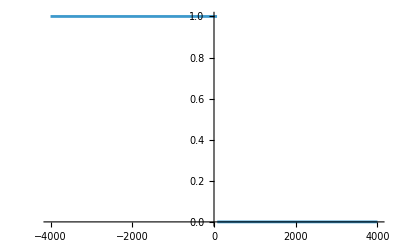

```mathematica
ysg[1,kxval,Bval]
Plot[HeavisideTheta[ysg[1,kxval,Bval]-y],{y,-4000,4000}]
```

## ΦB

### positive B

0.013487

{3990.23,1.87387×10^10,1.17996×10^17,8.06538×10^23}

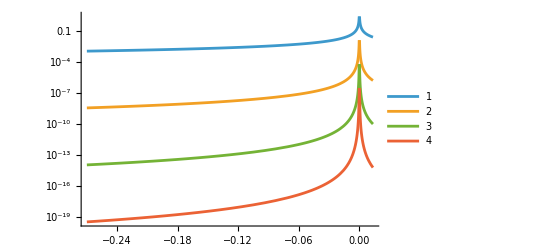

{2025.48,9.51195×10^9,5.98958×10^16,4.09406×10^23}

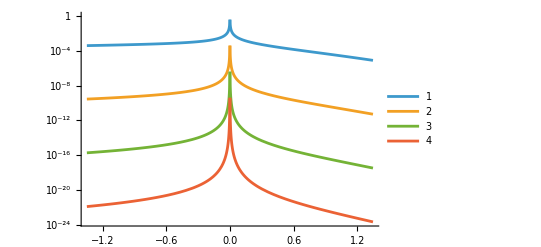

```mathematica
Bval=1.0(* 10^(-1)*)10^(2);kxval=N[2π *10^(-0)];a0val=1;
ratval=9;ylim=ysg[1,kxval,Bval]

Clear[fnb,int,normb];
	fnb[n_,y_]:=ϕB[a0val,y,(*ξ*)1,kxval,Bval, n,ratval](*(1+Erf[-Sign[Bval](y- ylim)])/2*)HeavisideTheta[Sign[Bval](ylim-y)];

normb[n_]:=Module[{int,yvar,lim=ysg[1,kxval,Bval]},
int=Quiet[NIntegrate[fnb[n,yvar]Conjugate[fnb[n,yvar]],{yvar,-2lim,2lim}]];
√int
];
lim=20 ylim;
{x1,x2,x3,x4}={normb[0],normb[1],normb[2],normb[3]}
(*Plot[(**)Abs[fn2[0,y]]/x1,{y,-2lim,2lim},PlotRange->All]*)
LogPlot[{(**)Abs[fnb[0,y]]/x1,Abs[fnb[1,y]]/x2,Abs[fnb[2,y]]/x3,Abs[fnb[3,y]]/x4},{y,-lim,lim},PlotRange->Automatic,PlotLegends->Automatic]
(*******using a smooth curoff rther than hard cut-off *******)

Clear[fnb,int,normb];
	fnb[n_,y_]:=ϕB[a0val,y,(*ξ*)1,kxval,Bval, n,ratval](1+Erf[-Sign[Bval](y- ylim)])/2;

normb[n_]:=Module[{int,yvar,lim=ysg[1,kxval,Bval]},
int=Quiet[NIntegrate[fnb[n,yvar]Conjugate[fnb[n,yvar]],{yvar,-2lim,2lim}]];
√int
];
lim=100 ylim;
{x1,x2,x3,x4}={normb[0],normb[1],normb[2],normb[3]}
(*Plot[(**)Abs[fn2[0,y]]/x1,{y,-2lim,2lim},PlotRange->All]*)
LogPlot[{(**)Abs[fnb[0,y]]/x1,Abs[fnb[1,y]]/x2,Abs[fnb[2,y]]/x3,Abs[fnb[3,y]]/x4},{y,-lim,lim},PlotRange->Automatic,PlotLegends->Automatic]
```

### negative B

-0.00666681

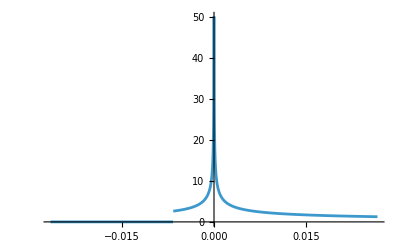

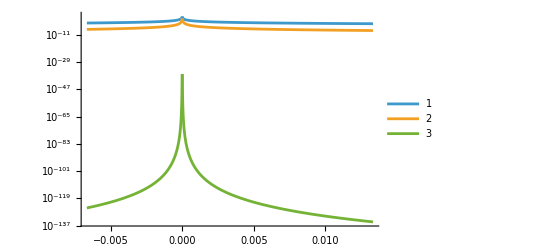

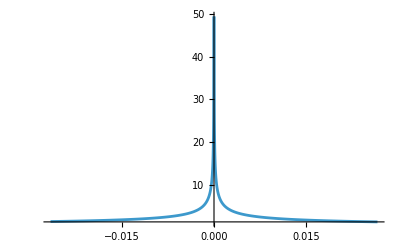

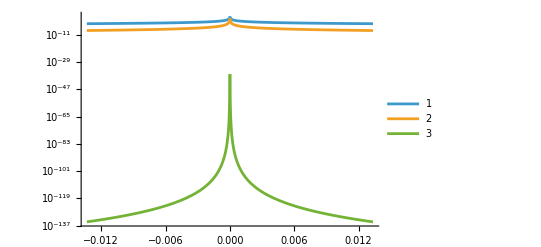

```mathematica
Bval=-1*10^(2);etaval=0;kxval=N[2π*0.00001];a0val=1;
ratval=1;ylim=ysg[1,kxval,Bval]

Clear[fnb,int,normb];
	fnb[n_,y_]=ϕB[a0val,vxval,y,(*ξ*)1,kxval,Bval, n,ratval]HeavisideTheta[Sign[Bval](ylim-y)];

normb[n_]:=Module[{int,yvar,limi=Abs[ysg[1,kxval,Bval]]},
int=Quiet[NIntegrate[fnb[n,yvar]Conjugate[fnb[n,yvar]],{yvar,-2limi,2limi}]];
√int
];
lim=2Abs[ylim];
{x1,x2,x3,x4}={normb[0],normb[1],normb[2],normb[30]};
Plot[Abs[fnb[0,y]]/x1,{y,-2Abs[lim],2Abs[lim]},PlotRange->All,PlotLegends->Automatic]

LogPlot[{(**)Abs[fnb[1,y]]/x2,Abs[fnb[2,y]]/x3,Abs[fnb[30,y]]/x4},{y,-lim,lim},PlotRange->All,PlotLegends->Automatic]
(*******using a smooth curoff rther than hard cut-off *******)
Clear[fnb,int,normb];
	fnb[n_,y_]=ϕB[a0val,y,(*ξ*)1,kxval,Bval, n,ratval](1+Erf[(Sign[Bval](ylim-y))/(√Abs[Bval])])/2;

normb[n_]:=Module[{int,yvar,limi=Abs[ysg[1,kxval,Bval]]},
int=Quiet[NIntegrate[fnb[n,yvar]Conjugate[fnb[n,yvar]],{yvar,-2limi,2limi}]];
√int
];
lim=2Abs[ylim];
{x1,x2,x3,x4}={normb[0],normb[1],normb[2],normb[30]};
Plot[Abs[fnb[0,y]]/x1,{y,-2Abs[lim],2Abs[lim]},PlotRange->All,PlotLegends->Automatic]

LogPlot[{(**)Abs[fnb[1,y]]/x2,Abs[fnb[2,y]]/x3,Abs[fnb[30,y]]/x4},{y,-lim,lim},PlotRange->All,PlotLegends->Automatic]
```

## ΦA

### positive B

{5.3278×10^8,4.24887×10^15,3.4205×10^22,2.72033×10^29}

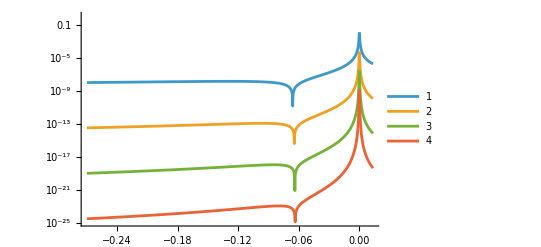

```mathematica
Bval=1.0(* 10^(-1)*)10^(2);kxval=N[2π *10^(-0)];a0val=1;vxval=1;
ratval=9;ylim=ysg[1,kxval,Bval];

Clear[fna,int,normb,norma,fnb];
	fna[n_,y_]:=ϕA[a0val,vxval,y,(*ξ*)1,kxval,Bval, n,ratval](*(1+Erf[-Sign[Bval](y- ylim)])/2*)HeavisideTheta[Sign[Bval](ylim-y)];

norma[n_]:=Block[{int,yvar,lim=ysg[1,kxval,Bval]},
int=Quiet[NIntegrate[fna[n,yvar]Conjugate[fna[n,yvar]],{yvar,-2lim,2lim}]];
√int
];
lim=20 ylim;
{x1,x2,x3,x4}={norma[0],norma[1],norma[2],norma[3]}
LogPlot[{(**)Abs[fna[0,y]]/x1,Abs[fna[1,y]]/x2,Abs[fna[2,y]]/x3,Abs[fna[3,y]]/x4},{y,-lim,lim},PlotRange->Automatic,PlotLegends->Automatic]
```

{2.70443×10^8,2.15676×10^15,1.73627×10^22,1.38086×10^29}

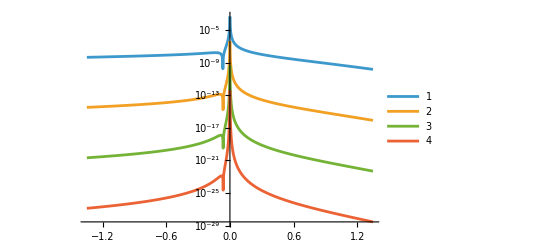

```mathematica
(*******using a smooth curoff rther than hard cut-off *******)

Clear[fna,int,normb];
	fna[n_,y_]:=ϕA[a0val,vxval,y,(*ξ*)1,kxval,Bval, n,ratval]((1+Erf[-Sign[Bval](y- ylim)])/2);

norma[n_]:=Module[{int,yvar,lim=ysg[1,kxval,Bval]},
int=Quiet[NIntegrate[fna[n,yvar]Conjugate[fna[n,yvar]],{yvar,-2lim,2lim}]];
√int
];
lim=100 ylim;
{x1,x2,x3,x4}={norma[0],norma[1],norma[2],norma[3]}
(*Plot[(**)Abs[fn2[0,y]]/x1,{y,-2lim,2lim},PlotRange->All]*)
LogPlot[{(**)Abs[fna[0,y]]/x1,Abs[fna[1,y]]/x2,Abs[fna[2,y]]/x3,Abs[fna[3,y]]/x4},{y,-lim,lim},PlotRange->Automatic,PlotLegends->Automatic]
```

### negative B

Power::infy: Infinite expression 1/(√0.) encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.0133336}}.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.0133336}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.0133336}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

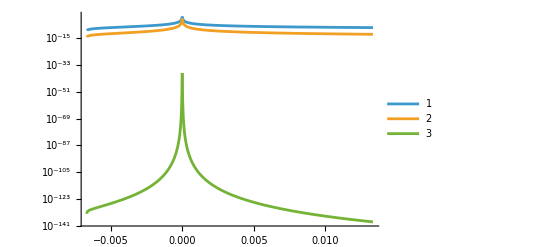

Power::infy: Infinite expression 1/(√0.) encountered.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.0133336}}.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.0133336}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumri: The integrand ComplexInfinity has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.0133336}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

-Graphics-

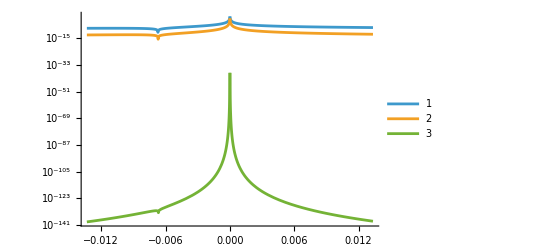

```mathematica
Bval=-1*10^(2);etaval=0;kxval=N[2π*0.00001];a0val=1;vxval=1;
ratval=1;ylim=ysg[1,kxval,Bval];

Clear[fna,int,norma];
	fna[n_,y_]=ϕA[a0val,vxval,y,(*ξ*)1,kxval,Bval, n,ratval]HeavisideTheta[Sign[Bval](ylim-y)];

norma[n_]:=Module[{int,yvar,limi=Abs[ysg[1,kxval,Bval]]},
int=Quiet[NIntegrate[fna[n,yvar]Conjugate[fna[n,yvar]],{yvar,-2limi,2limi}]];
√int
];
lim=2Abs[ylim];
{x1,x2,x3,x4}={norma[0],norma[1],norma[2],norma[30]};
Plot[Abs[fna[0,y]]/x1,{y,-2Abs[lim],2Abs[lim]},PlotRange->All,PlotLegends->Automatic]

LogPlot[{(**)Abs[fna[1,y]]/x2,Abs[fna[2,y]]/x3,Abs[fna[30,y]]/x4},{y,-lim,lim},PlotRange->All,PlotLegends->Automatic]
(*******using a smooth curoff rther than hard cut-off *******)
Clear[fna,int,norma];
	fna[n_,y_]=ϕA[a0val,vxval,y,(*ξ*)1,kxval,Bval, n,ratval]((1+Erf[(Sign[Bval](ylim-y))/(√Abs[Bval])])/2);

norma[n_]:=Module[{int,yvar,limi=Abs[ysg[1,kxval,Bval]]},
int=Quiet[NIntegrate[fna[n,yvar]Conjugate[fna[n,yvar]],{yvar,-2limi,2limi}]];
√int
];
lim=2Abs[ylim];
{x1,x2,x3,x4}={norma[0],norma[1],norma[2],norma[30]};
Plot[Abs[fna[0,y]]/x1,{y,-2Abs[lim],2Abs[lim]},PlotRange->All,PlotLegends->Automatic]

LogPlot[{(**)Abs[fna[1,y]]/x2,Abs[fna[2,y]]/x3,Abs[fna[30,y]]/x4},{y,-lim,lim},PlotRange->All,PlotLegends->Automatic]
```

## Total wvfn

### positive B

{5.3278×10^8,4.24887×10^15,3.4205×10^22,2.72033×10^29}

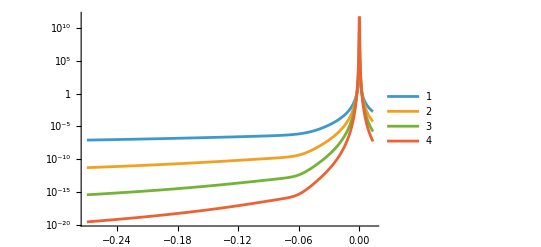

```mathematica
Bval=1.0(* 10^(-1)*)10^(2);kxval=N[2π *10^(-0)];a0val=1;vxval=1;
ratval=9;ylim=ysg[1,kxval,Bval];

Clear[int,norm,vec];
	vec[n_,y_]:={ϕA[a0val,vxval,y,(*ξ*)1,kxval,Bval, n,ratval],ϕB[a0val,y,(*ξ*)1,kxval,Bval, n,ratval]}HeavisideTheta[Sign[Bval](ylim-y)];

norm[n_]:=Block[{int,yvar,lim=ysg[1,kxval,Bval]},
int=Quiet[NIntegrate[Conjugate[vec[n,yvar]].vec[n,yvar],{yvar,-2lim,2lim}]];
√int
];
lim=20 ylim;
{x1,x2,x3,x4}={norm[0],norm[1],norm[2],norm[3]}
LogPlot[{(**)Conjugate[vec[0,y]].vec[0,y]/x1,Conjugate[vec[1,y]].vec[1,y]/x2,Conjugate[vec[2,y]].vec[2,y]/x3,Conjugate[vec[3,y]].vec[3,y]/x4},{y,-lim,lim},PlotRange->Automatic,PlotLegends->Automatic]
```

{2.70443×10^8,2.15676×10^15,1.73627×10^22,1.38086×10^29}

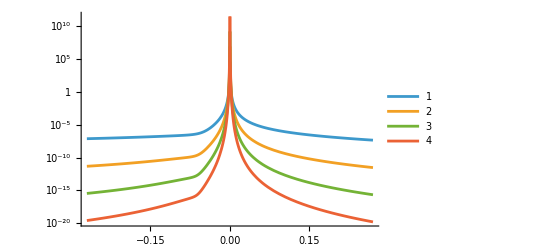

```mathematica
(*******using a smooth curoff rther than hard cut-off *******)
Bval=1.0(* 10^(-1)*)10^(2);kxval=N[2π *10^(-0)];a0val=1;vxval=1;
ratval=9;ylim=ysg[1,kxval,Bval];

Clear[fna,int,norm,vec];
	vec[n_,y_]:={ϕA[a0val,vxval,y,(*ξ*)1,kxval,Bval, n,ratval],ϕB[a0val,y,(*ξ*)1,kxval,Bval, n,ratval]}((1+Erf[-Sign[Bval](y- ylim)])/2);

norm[n_]:=Block[{int,yvar,lim=ysg[1,kxval,Bval]},
int=Quiet[NIntegrate[Conjugate[vec[n,yvar]].vec[n,yvar],{yvar,-2lim,2lim}]];
√int
];

lim=20 ylim;
{x1,x2,x3,x4}={norm[0],norm[1],norm[2],norm[3]}
LogPlot[{(**)Conjugate[vec[0,y]].vec[0,y]/x1,Conjugate[vec[1,y]].vec[1,y]/x2,Conjugate[vec[2,y]].vec[2,y]/x3,Conjugate[vec[3,y]].vec[3,y]/x4},{y,-lim,lim},PlotRange->Automatic,PlotLegends->Automatic]
```

### negative B

-0.00666681

{3.06185×10^11,3.0861×10^18,5.805773070146896×10^219}

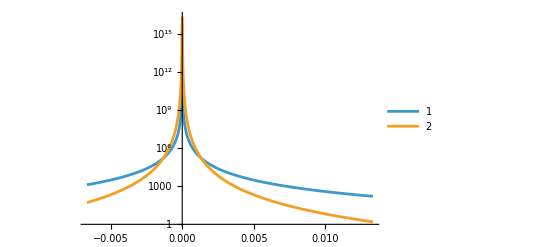

```mathematica
Bval=-1*10^(2);etaval=0;kxval=N[2π*0.00001];a0val=1;vxval=0.0004;
ratval=1;ylim=ysg[1,kxval,Bval]
Clear[int,norm,vec,limi,lim];
	vec[n_,y_]:={ϕA[a0val,vxval,y,(*ξ*)1,kxval,Bval, n,ratval],ϕB[a0val,y,(*ξ*)1,kxval,Bval, n,ratval]}HeavisideTheta[Sign[Bval](ylim-y)];

norm[n_]:=Block[{int,yvar,limi=Abs[ysg[1,kxval,Bval]]},
int=Quiet[NIntegrate[Conjugate[vec[n,yvar]].vec[n,yvar],{yvar,-2limi,2limi}]];
√int
];

lim=2Abs[ylim];
{x2,x3,x4}={norm[1],norm[2],norm[30]}

LogPlot[{(**)Conjugate[vec[1,y]].vec[1,y]/x2,Conjugate[vec[2,y]].vec[2,y]/x3},{y,-lim,lim},PlotRange->All,PlotLegends->Automatic]
```